1. Calculate the sine of the golden angle (with a calculator-like output). 
(Hint: Sin, GoldenAngle)

```mathematica
(*solution 1*)
Sin[GoldenAngle]//N
```

0.67549

```mathematica
(*solution 2*)
N[Sin[GoldenAngle]]
```

0.67549

```mathematica
(*solution 3*)
N@Sin[GoldenAngle]
```

0.67549

```mathematica
(*solution 4*)
Sin[N[GoldenAngle]]
```

0.67549

2. (1)Create a list of five objects and randomly choose one of them. (2)Then replace the third object in the list with a new object. (3)Check the new list. 
(Hint: RandomChoice)

```mathematica
myList = {"one","two","three","four","five"}
```

{one,two,three,four,five}

```mathematica
RandomChoice[myList]
```

two

```mathematica
myList[[3]] = "lkajsdflkasdjflksj"
```

lkajsdflkasdjflksj

```mathematica
myList
```

{one,two,lkajsdflkasdjflksj,four,five}

3. Automatically create nine fractions in the form 1/2, 1/3, 1/4,…,1/10. Automatically calculate the sum of the list (as a decimal approximation).
(Hint: Table, Total)

```mathematica
myList = Table[1/n,{n,2,10}]
(*Talble[pattern,{variableInPattern,start,end}]*)
```

{1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10}

```mathematica
Total[myList]
```

4861/2520

4.Use the previous problem as an example. 

(1)Create 100 ratios of Fibonacci numbers, such that each ratio is a Fibonacci number divided by its neighbor on the left (starting with the second Fibonacci number). Since the Fibonacci sequence is (1, 1, 2, 3,...), the required sequence should be (1/1, 2/1, 3/2,…). 

(2)Plot the list. The sequence should approach a definite limit (which happens to be the golden ratio or 1.6…). 

(Hint: Fibonacci, Table, ListLinePlot)

```mathematica
(*N+1,N*)
```

```mathematica
myList = Table[Fibonacci[n+1]/Fibonacci[n],{n,1,100}]
```

{1,2,3/2,5/3,8/5,13/8,21/13,34/21,55/34,89/55,144/89,233/144,377/233,610/377,987/610,1597/987,2584/1597,4181/2584,6765/4181,10946/6765,17711/10946,28657/17711,46368/28657,75025/46368,121393/75025,196418/121393,317811/196418,514229/317811,832040/514229,1346269/832040,2178309/1346269,3524578/2178309,5702887/3524578,9227465/5702887,14930352/9227465,24157817/14930352,39088169/24157817,63245986/39088169,102334155/63245986,165580141/102334155,267914296/165580141,433494437/267914296,701408733/433494437,1134903170/701408733,1836311903/1134903170,2971215073/1836311903,4807526976/2971215073,7778742049/4807526976,12586269025/7778742049,20365011074/12586269025,32951280099/20365011074,53316291173/32951280099,86267571272/53316291173,139583862445/86267571272,225851433717/139583862445,365435296162/225851433717,591286729879/365435296162,956722026041/591286729879,1548008755920/956722026041,2504730781961/1548008755920,4052739537881/2504730781961,6557470319842/4052739537881,10610209857723/6557470319842,17167680177565/10610209857723,27777890035288/17167680177565,44945570212853/27777890035288,72723460248141/44945570212853,117669030460994/72723460248141,190392490709135/117669030460994,308061521170129/190392490709135,498454011879264/308061521170129,806515533049393/498454011879264,1304969544928657/806515533049393,2111485077978050/1304969544928657,3416454622906707/2111485077978050,5527939700884757/3416454622906707,8944394323791464/5527939700884757,14472334024676221/8944394323791464,23416728348467685/14472334024676221,37889062373143906/23416728348467685,61305790721611591/37889062373143906,99194853094755497/61305790721611591,160500643816367088/99194853094755497,259695496911122585/160500643816367088,420196140727489673/259695496911122585,679891637638612258/420196140727489673,1100087778366101931/679891637638612258,1779979416004714189/1100087778366101931,2880067194370816120/1779979416004714189,4660046610375530309/2880067194370816120,7540113804746346429/4660046610375530309,12200160415121876738/7540113804746346429,19740274219868223167/12200160415121876738,31940434634990099905/19740274219868223167,51680708854858323072/31940434634990099905,83621143489848422977/51680708854858323072,135301852344706746049/83621143489848422977,218922995834555169026/135301852344706746049,354224848179261915075/218922995834555169026,573147844013817084101/354224848179261915075}

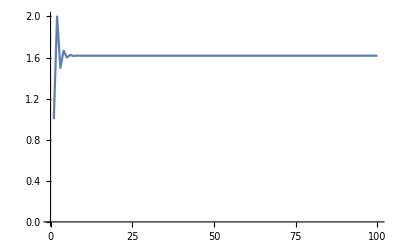

```mathematica
ListLinePlot[myList]
```

```mathematica
573147844013817084101/354224848179261915075 // N
```

1.61803

5. Plot the function that is the sine of the sine of the sine of x, where x ranges from -2π to 2π. (Hint: Plot)

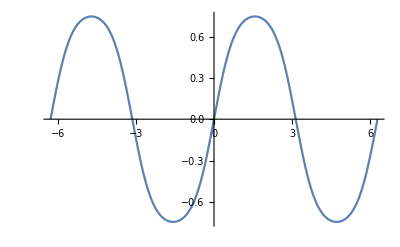

```mathematica
Plot[Sin[Sin[Sin[n]]],{n,-2*Pi,2*Pi}]
```

```mathematica
|
```

```mathematica
(Sin@Sin[n]//Sin)~Plot~{n,-2*Pi,2*Pi}
```

-Graphics-

```mathematica
N[Pi]
```

3.14159

```mathematica
N[Pi,3]
```

6. Find if you were born in a prime year. (Hint: PrimeQ)

```mathematica
PrimeQ[1999]
```

True

7. Create a loop that prints the squares of the first 10 natural numbers (1, 2, 3,…). (Hint: For) 

{1,4,9,16,25,36,49,64,81,100}

```mathematica
For[i = 1,i≤10,i++,Print[i*i]]
```

1

4

9

16

25

36

49

64

81

100

8. Create a list of your five friends.Use a loop to produce automatic greetings for each one of them.For example,if the initial list is (Joe,Jane,…),the output should be ("Hi Joe!","Hi Jane!",…).(Hint:For,indexing)

```mathematica
myFriends = {"A","B","C","D","E"}
```

{A,B,C,D,E}

```mathematica
myFriends[[2]]
```

B

```mathematica
For[i = 1,i≤5,i++,Print["Hi "   ,     myFriends[[i]]   ,    "!"]]
(* "Hi " "A" "!"      *)
```

HiA!

HiB!

HiC!

HiD!

HiE!

9. Run the command Pi = 3.14. Explain its result. Now run the command Pi == 3.14. Explain this new result.

```mathematica
Pi = 3.14
```

Set::wrsym: Symbol π is Protected.

3.14

```mathematica
Pi == 3.14
Pi ≤ 3.14
Pi ≥ 3.14
Pi < 3.14
Pi >3.14
```

False

```mathematica
N[Pi,100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

10. Run the following command: 

RegionPlot3D[True, {x, 0, 1}, {y, 0, 1}, {z, 0, 1}, AxesLabel -> {x, y, z}, RotationAction -> “Clip”] 

Now try: 

RegionPlot3D[x > 0.5, {x, 0, 1}, {y, 0, 1}, {z, 0, 1}, AxesLabel -> {x, y, z}, RotationAction -> “Clip”]. 

What does the function do? “Sculpt” with various logical conditions on x, y, and z (==, >, &&, ||, etc.). The purpose of this exercise is to practice logical operations.

```mathematica
RegionPlot3D[True,{x,0,1},{y,0,1},{z,0,1},AxesLabel->{x,y,z},RotationAction->"Clip"]
```

-Graphics3D-

```mathematica
RegionPlot3D[x > 0.5, {x, 0, 1}, {y, 0, 1}, {z, 0, 1}, AxesLabel -> {x, y, z}, RotationAction -> "Clip"]
```

-Graphics3D-

```mathematica
RegionPlot3D[x*x*x > 0.5 &&  y*y*y > 0.5 , {x, 0, 1}, {y, 0, 1}, {z, 0, 1}, AxesLabel -> {x, y, z}, RotationAction -> "Clip"]
```

-Graphics3D-